```mathematica
fsz=22;16;
(*path=NotebookDirectory[]<>"figures/"*)
fontFamilyPB="Latin Modern Math";"Helvetica";
fontFamily="Times New Roman";FontSize->24;

SetOptions[Plot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLinearPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[Graphics,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];


lineStyle=Dashing[{1,0}];Automatic;xRPlotMin=0;ar=1;gridLines=Automatic;imSz=400;
pltStl={{lineStyle,Blue,Thickness[thickness=.013/2]},{lineStyle,RGBColor[0.7,0.3,0.0],Thickness[thickness]},{lineStyle,RGBColor[0.9,0.5,0.6],Thickness[thickness]},{lineStyle,Brown,Thickness[thickness]},{lineStyle,Black,Thickness[thickness]}};
```

```mathematica
Clear[F,B,O2,B0,C0,Func,M];
```

```mathematica
Func:=Module[{f,g,eqs,BC,DEq,solg,sol,rts,Evs},
f=HeavisideTheta[R[t]-R0]α A[t](R[t]-R0);
g=ϵ A[t]R[t]HeavisideTheta[R1-R[t]]+ϵ A[t] R1 HeavisideTheta[R[t]-R1];

eqs={R'[t] == -f-g-ξ ω R[t] G[t]+σ1,
G'[t]== ((1-ξ)ω R[t] - a1) G[t],
H'[t]==  ((1-ψ)Ω CH[t] - a2) H[t],
L'[t]== f - β B[t] L[t]+ξ ω R[t] G[t],
CO'[t]==μ O2[t] g + γ λ O2[t] CH[t] F[t]+ψ Ω CH[t] H[t],
CH'[t] == κ β B[t] L[t] - γ O2[t] CH[t] F[t],
O2'[t] == -(μ O2[t] g + γ λ O2[t] CH[t] F[t])+σ2,
A'[t] == (1-μ)O2[t]g - s A[t],
B'[t]==((1-κ) β L[t] -u) B[t],
F'[t] == ((1-λ)γ O2[t] CH[t]-ν)F[t]};
BC = {R[0]==RI,L[0]==0,CO[0]==0,CH[0]==0,A[0]==A0,B[0]==B0,F[0]==C0,O2[0]==O20,G[0]==G0,H[0]==H0};
Evs={WhenEvent[O2'[t]==0,Sow[t]]};
DEq = Flatten[{eqs,BC,Evs}];
solg=Reap[NDSolve[DEq,{A,B,F,O2',CH',L',CO',R',O2,CH,L,CO,R,G,H},{t,0,Tmax},PrecisionGoal->10]];
sol =solg[[1]];
rts = solg[[2]];
{First[sol],First[rts]}

]
```

```mathematica
R0=2.5;
R1=1;

a2 = 0.5;
a1=0.5; (* 0.1  *)
s=0.1;
ν=0.1;
u=0.1;

λ=0.5; 
κ=0.5;
μ=0.5;
ξ=0.5; (* 0.5 *)
ψ=0.5;

A0=1.;
H0=1; (*1? *)
G0=1;
B0=1;
C0=1;

β=0.5; 
α=0.5; (* 0.5 *)
ω=0.02; (* 0.02 *)
Ω=0.02;
ϵ=0.5;
γ=0.5;
```

#### Oscillation qualitative analysis

```mathematica
RI=10;
O20=1;
σ1 = 1; (* resource rate  0 for oxygen impulse only *)
σ2 = 0.15; (* oxygen rate 0 for resource impulse only *)
(*σ2 = 0.10991;*)
ta = ConstantArray[0,Length[Range[0.1,0.2,0.001]]];
ii=1;
tt=Table[
σ2 = 0.1+i; (* oxygen rate 0.15 *)
If[i<0.09,cut=6;Tmax=400;,cut=6;Tmax=550];
{sol,rts}  = Func;
tx = 97;
ta[[ii]]=O2[rts[[4]]]-O2[rts[[5]]]/.sol;
ii=ii+1;
(*Print[Show[Plot[O2[t]/.sol,{t,0,Tmax}]]];
Print[rts];*)
Tper=rts[[5;;cut]]-RotateRight[rts,2][[5;;cut]];
(*Print[rts[[5;;cut]]];
Print[RotateRight[rts,2][[5;;cut]]];
Print[Tper];*)
m = First[Tper];
st =StandardDeviation[Tper];
{σ2,m}
,{i,0,0.1,0.001}];
ta
tt
```

{1.27747,1.25791,1.23845,1.21909,1.19983,1.18067,1.1616,1.14263,1.12374,1.10494,1.08623,1.0676,1.04906,1.03059,1.0122,0.993887,0.975648,0.957482,0.939388,0.921364,0.903411,0.885526,0.86771,0.849963,0.832283,0.814671,0.797127,0.779652,0.762246,0.74491,0.727645,0.710453,0.693335,0.676294,0.65933,0.642448,0.62565,0.608939,0.592318,0.575792,0.559364,0.54304,0.526824,0.510722,0.49474,0.478883,0.463159,0.447574,0.432135,0.416851,0.401728,0.386776,0.372002,0.357415,0.343024,0.328839,0.314867,0.301119,0.287603,0.274329,0.261306,0.248541,0.236045,0.223825,0.21189,0.200248,0.188905,0.17787,0.167148,0.156747,0.146671,0.136926,0.127517,0.118447,0.109721,0.10134,0.0933082,0.0856258,0.0782941,0.0713134,0.0646833,0.0584026,0.0524697,0.0468818,0.0416357,0.0367276,0.0321527,0.0279057,0.0239805,0.0203708,0.0170694,0.0140688,0.0113617,0.00894065,0.00679881,0.00493066,0.003333,0.00200734,0.000964189,0.00023835,0.000506882}

{{0.1,84.0141},{0.101,83.4069},{0.102,82.8108},{0.103,82.2256},{0.104,81.6509},{0.105,81.0866},{0.106,80.5325},{0.107,79.9885},{0.108,79.4544},{0.109,78.9302},{0.11,78.4157},{0.111,77.9107},{0.112,77.4152},{0.113,76.9294},{0.114,76.4532},{0.115,75.9862},{0.116,75.5286},{0.117,75.0803},{0.118,74.6412},{0.119,74.2114},{0.12,73.791},{0.121,73.3796},{0.122,72.9774},{0.123,72.5842},{0.124,72.2002},{0.125,71.8256},{0.126,71.4598},{0.127,71.103},{0.128,70.7553},{0.129,70.4165},{0.13,70.0868},{0.131,69.7659},{0.132,69.4539},{0.133,69.1508},{0.134,68.8563},{0.135,68.5706},{0.136,68.2935},{0.137,68.0249},{0.138,67.7649},{0.139,67.5132},{0.14,67.27},{0.141,67.035},{0.142,66.8081},{0.143,66.5895},{0.144,66.3791},{0.145,66.1766},{0.146,65.982},{0.147,65.7952},{0.148,65.6162},{0.149,65.445},{0.15,65.2813},{0.151,65.1253},{0.152,64.9769},{0.153,64.8359},{0.154,64.7023},{0.155,64.5762},{0.156,64.4574},{0.157,64.3459},{0.158,64.2418},{0.159,64.1448},{0.16,64.0551},{0.161,63.9726},{0.162,63.8973},{0.163,63.829},{0.164,63.7679},{0.165,63.7138},{0.166,63.6666},{0.167,63.6264},{0.168,63.5929},{0.169,63.5662},{0.17,63.546},{0.171,63.5322},{0.172,63.5246},{0.173,63.5228},{0.174,63.5266},{0.175,63.5355},{0.176,63.5489},{0.177,63.5662},{0.178,63.5866},{0.179,63.6091},{0.18,63.6325},{0.181,63.6552},{0.182,63.6756},{0.183,63.6913},{0.184,63.7001},{0.185,63.6987},{0.186,63.6837},{0.187,63.651},{0.188,63.596},{0.189,63.5131},{0.19,63.3964},{0.191,63.2388},{0.192,63.032},{0.193,62.766},{0.194,62.4278},{0.195,61.9997},{0.196,61.4544},{0.197,60.7452},{0.198,59.7756},{0.199,58.2575},{0.2,103.987}}

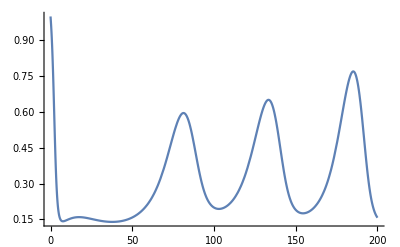

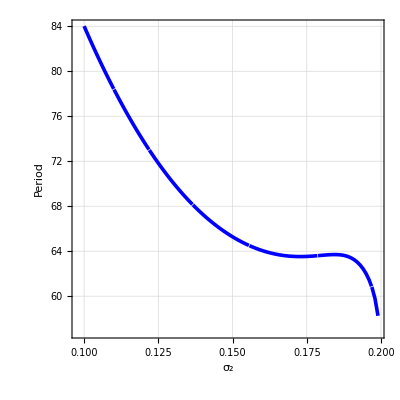

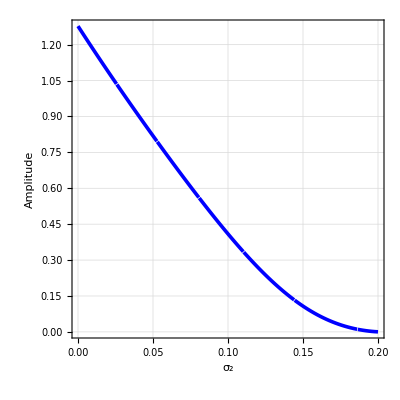

```mathematica
σ2=0.15;
{sol,rts}=Func;
Plot[O2[t]/.sol,{t,0,200},PlotRange->All]
ttplot=Quiet@ListLinePlot[tt[[;;Length[tt]-1]],
PlotRange->All,AspectRatio->1,(*ImageSize->250,*)FrameLabel->{"σ_2","Period"},
ImageSize->imSz,Axes->None,PlotStyle->pltStl,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->fsz},FrameStyle->Thick,FrameTicksStyle->Black,LabelStyle->Black,GridLines->gridLines,AspectRatio->ar
]
taplot=Quiet@ListLinePlot[ta[[;;Length[tt]-1]],
PlotRange->All,AspectRatio->1,(*ImageSize->250,*)FrameLabel->{"σ_2","Amplitude"},
ImageSize->imSz,Axes->None,PlotStyle->pltStl,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->fsz},FrameStyle->Thick,FrameTicksStyle->Black,LabelStyle->Black,GridLines->gridLines,AspectRatio->ar,DataRange->{0,0.2}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
ttf = tt;
taf = Transpose@Join[{Range[0.1,0.2,0.001]},{ta}];
Export["period_vs_sigma2.pdf",ttplot]
Export["amplitude_vs_sigma2.pdf",taplot]
Export["period_vs_sigma2.csv",ttf]
Export["amplitude_vs_sigma2.csv",taf]
```

period_vs_sigma2.pdf

amplitude_vs_sigma2.pdf

period_vs_sigma2.csv

amplitude_vs_sigma2.csv

```mathematica
ta
```

{1.27747,1.25791,1.23845,1.21909,1.19983,1.18067,1.1616,1.14263,1.12374,1.10494,1.08623,1.0676,1.04906,1.03059,1.0122,0.993887,0.975648,0.957482,0.939388,0.921364,0.903411,0.885526,0.86771,0.849963,0.832283,0.814671,0.797127,0.779652,0.762246,0.74491,0.727645,0.710453,0.693335,0.676294,0.65933,0.642448,0.62565,0.608939,0.592318,0.575792,0.559364,0.54304,0.526824,0.510722,0.49474,0.478883,0.463159,0.447574,0.432135,0.416851,0.401728,0.386776,0.372002,0.357415,0.343024,0.328839,0.314867,0.301119,0.287603,0.274329,0.261306,0.248541,0.236045,0.223825,0.21189,0.200248,0.188905,0.17787,0.167148,0.156747,0.146671,0.136926,0.127517,0.118447,0.109721,0.10134,0.0933082,0.0856258,0.0782941,0.0713134,0.0646833,0.0584026,0.0524697,0.0468818,0.0416357,0.0367276,0.0321527,0.0279057,0.0239805,0.0203708,0.0170694,0.0140688,0.0113617,0.00894065,0.00679881,0.00493066,0.003333,0.00200734,0.000964189,0.00023835,0.000506882}